# Bifurcation Diagram of the xapAB Circuit

Kathrin Laxhuber, 2020

## Init

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
inch = 72;
```

### Package Imports

```mathematica
<<MaTeX`
```

```mathematica
ConfigureMaTeX["pdfLaTeX"->"C:/Program Files/MiKTeX 2.9/miktex/bin/x64/pdflatex.exe","Ghostscript"->"C:/Program Files/gs/gs9.26/bin/gswin64c.exe"];
```

### Plot Options

```mathematica
plotOptionsBasic={Frame->True,FrameStyle->BlackFrame};
```

```mathematica
texStyle={FontFamily->"Times",FontSize->11};
plotSizesLaTeX=<|"Normal"->350,"Two"->250,"Three"->180|>;
```

### System ODE’s

```mathematica
ActiveXapR[x_,XapR_,ϵx_,KA_,KI_]:=XapR (1+x/KA)^2/((1+x/KA)^2+Exp[ϵx] (1+x/KI)^2);

dpdt[p_,x_,params_]:=params[["ρ"]] (
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]]
)/(
1+
2 ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]+
ActiveXapR[x,params[["XapR"]],params[["ϵ_x"]],params[["K_χA"]],params[["K_χI"]]]^2
Exp[params[["ϵ_coop"]]]
)-p;

dxdt[p_,x_,params_]:= (params[["k_(β, i)"]] (params[["c"]])/(params[["K_(β, i)"]]+params[["c"]])-params[["k_(β, e)"]] (x)/(params[["K_(β, e)"]]+x)-params[["k_α"]] (x)/(1+x)) p+params[["k_η"]](params[["c"]]-params[["ξ"]] x);
```

### Parameters

```mathematica
params2d=<|"ρ"->10^(-2),"XapR"->10^(0),"c"->13,"k_(β, i)"->5 10^4,"k_(β, e)"->10^3,"k_α"->10^2,"k_η"->5 10^(-1),"K_(β, i)"->10^1,"K_(β, e)"->10^2,"K_χA"->10^2,"K_χI"->10^4,"ξ"-> 0.8,"ϵ_x"->5,"ϵ_coop"->5|>;
```

## Deterministic Bifurcation Diagram

### Function Definition for Finding Zeroes

```mathematica
SteadyStateSolver::usage="Calculates the numerical Steady-state solution to the set of two ODE's.

Arguments:
RHS of the ODE's: {dpdt,dxdt}
parameters: association of parameters

Returns:
List of the solutions {p->...,x->...}";
```

```mathematica
SteadyStateSolver[{dpdt_,dxdt_},params_]:=Module[{p,x,pres,xres},
(* Solve x-ODE for p and enter into p-ODE and solve for x *)
pres = Solve[dxdt[p,x,params]==0,p][[All,1,2]];
xres = {};
Do[AppendTo[xres,NSolve[dpdt[p,x,params]==0,x][[All]]],{p,pres}];
xres=xres[[1]];

(* Update result for p *)
pres = {};
Do[AppendTo[pres,NSolve[dxdt[p,x,params]==0,p][[All,1]]],{x,xres[[All,1,2]]}];

(* Return result *)
Return[Join[pres,xres,2]]
]
```

```mathematica
SelectSols::usage="Returns only positive real solutions.

Arguments:
solutions: List of solutions {p,x} to the ODE's in question.
c: value of the parameter c (nondimensional extracellular concentration)

Returns:
low (1 low solution), high (1 high solution), bi (3 solutions) or border (2 solutions) (as a string)

Caution: this cannot handle roots with multiplicity greater than one.";
```

```mathematica
(* SelectSols::counting = "The number of solutions `1`+`2`+`3` does not equal 5 or the complex solutions do not appear in pairs."; *)
```

```mathematica
SelectSols[sols_]:=Module[{possols,negsols,complexsols,poscount,negcount,complexcount,stability},
Catch[
(* Finding solutions *)
possols=Cases[sols[[All,All,2]],{_?NonNegative,_?NonNegative}];
negsols=Cases[sols[[All,All,2]],{_?Negative,_?NonNegative}|{_?NonNegative,_?Negative}|{_?Negative,_?Negative}];
complexsols=Select[sols[[All,All,2]] ,Not[#∈Reals]&];

(* Counting solutions *)
poscount=Length[possols];
negcount=Length[negsols];
complexcount=Length[complexsols];

(* Error prevention *)
(* If[poscount+negcount+complexcount===5 && Mod[complexcount,2]===0,,Throw[Message[SelectSols::counting,poscount,negcount,complexcount]]]; *)

(* Returning the positive, real solutions *)
Return[possols]
]]
```

### Plotting

```mathematica
ConcList= Range[5,28,0.05];
paramsC=Table[Append[params2d,<|"c"->conc|>],{conc,ConcList}];
FixedPointsList=Flatten[Table[{ConcList[[i]],#}&/@SelectSols[SteadyStateSolver[{dpdt,dxdt},paramsC[[i]]]][[All,1]],{i,1,Length[ConcList]}],1];
```

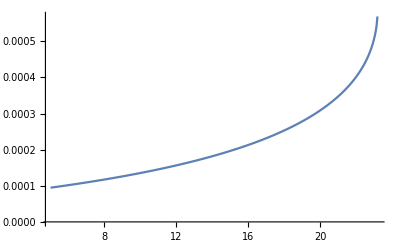

```mathematica
DetPlot1=ListLinePlot[SortBy[FixedPointsList,#[[2]]&][[1;;365]]]
```

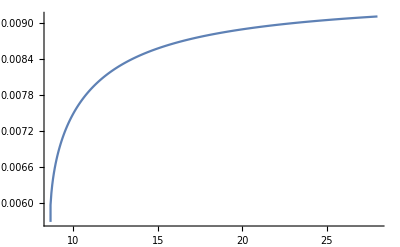

```mathematica
DetPlot2=ListLinePlot[SortBy[FixedPointsList,#[[2]]&][[620;;]]]
```

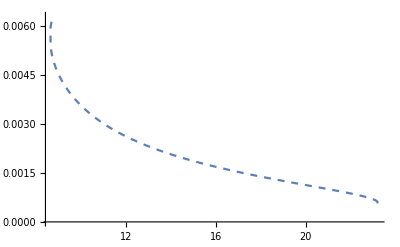

```mathematica
DetPlot3=ListLinePlot[SortBy[FixedPointsList,#[[2]]&][[365;;660]],PlotStyle->Dashed]
```

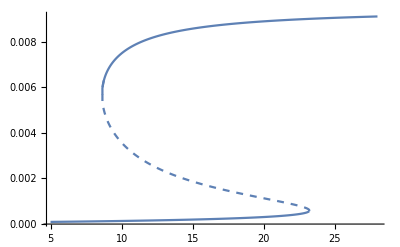

```mathematica
DetPlot=Show[DetPlot1,DetPlot2,DetPlot3,PlotRange->All]
```

## Comparing to StochPy Simulations

### Estimated Splitting of the Bimodal’s

```mathematica
UpList=Import["PythonExport/Paper/Bimodal.csv"][[7;;]][[;;,2]];
```

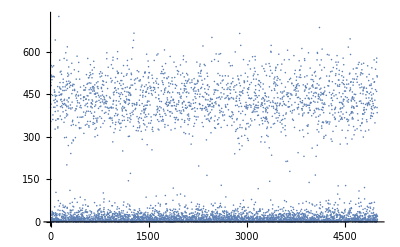

```mathematica
ListPlot[UpList]
```

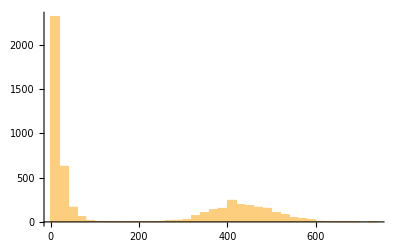

```mathematica
Histogram[UpList,25]
```

```mathematica
hist=HistogramList[UpList,25]
```

{{0,20,40,60,80,100,120,140,160,180,200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,620,640,660,680,700,720,740},{2317,630,168,61,14,6,5,2,4,1,3,3,6,11,20,28,68,103,137,154,246,192,181,168,155,106,78,49,39,25,9,3,4,2,1,0,1}}

```mathematica
MinDetect[hist[[2]]]
```

{0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,0}

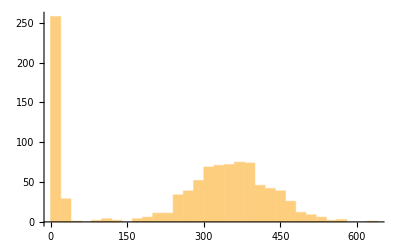

```mathematica
Histogram[DownList,25]
```

```mathematica
hist2=HistogramList[DownList,25]
```

{{0,20,40,60,80,100,120,140,160,180,200,220,240,260,280,300,320,340,360,380,400,420,440,460,480,500,520,540,560,580,600,620,640},{258,29,1,0,2,4,2,0,4,6,11,11,34,39,52,69,71,72,75,74,46,42,39,26,12,9,6,2,3,0,0,1}}

```mathematica
MinDetect[hist2[[2]]]
```

{0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,1,1,0}

### Basic Plot

```mathematica
ConcListStochUp={12,18.5,25};
MeanListStochUp={Mean[Import["PythonExport/Paper/Low.csv"][[7;;]][[;;,2]]],Mean[Import["PythonExport/Paper/Bimodal.csv"][[7;;]][[;;,2]]],Mean[Import["PythonExport/Paper/High.csv"][[7;;]][[;;,2]]]}/(5 10^4);
PlotDataStochUp=Table[{ConcListStochUp[[i]],MeanListStochUp[[i]]},{i,1,Length[ConcListStochUp]}];
```

```mathematica
UpList=Import["PythonExport/Paper/Bimodal.csv"][[7;;]][[;;,2]];
BimodalUp=Mean/@{Select[UpList,#≤ 160&],Select[UpList,#>160&]}/(5 10^4);
PlotBimodalUp=Table[{18.5,BimodalUp[[i]]},{i,1,Length[BimodalUp]}];
```

```mathematica
ConcListStochDown={12,10,9};
MeanListStochDown={Mean[Import["PythonExport/Paper/Hysteresis1.csv"][[7;;]][[;;,2]]],Mean[Import["PythonExport/Paper/Hysteresis2.csv"][[7;;]][[;;,2]]],Mean[Import["PythonExport/Paper/Hysteresis3.csv"][[7;;]][[;;,2]]]}/(5 10^4);
PlotDataStochDown=Table[{ConcListStochDown[[i]],MeanListStochDown[[i]]},{i,1,Length[ConcListStochDown]}];
```

```mathematica
DownList=Import["PythonExport/Paper/Hysteresis2.csv"][[7;;]][[;;,2]];
BimodalDown=Mean/@{Select[DownList,#≤ 60&],Select[DownList,#>60&]}/(5 10^4);
PlotBimodalDown=Table[{10,BimodalDown[[i]]},{i,1,Length[BimodalDown]}];
```

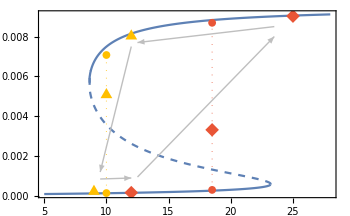

```mathematica
BifurcationPlot=Show[DetPlot,
ListPlot[{PlotDataStochUp,PlotDataStochDown},PlotStyle->{ColorData[97,11],ColorData[97,8]},PlotMarkers->{{◆,14},{▲,14}},PlotLegends->Placed[{MaTeX["\\begin{aligned} &\\mathrm{Simulation \\ started \\ at} \\\\ &\\mathrm{[m]_a=[p]_a=[x]_a}=0 \\end{aligned}","FontSize"->14],MaTeX["\\begin{aligned} &\\mathrm{Simulation \\ started \\ at} \\\\ &\\mathrm{the \\ upper \\ fixed \\ point} \\end{aligned}","FontSize"->14]},Right]],
ListPlot[{PlotBimodalUp,PlotBimodalDown},PlotStyle->{ColorData[97,11],ColorData[97,8]},PlotMarkers->{•,8}],
Graphics[{{Dotted,Thickness[0.002],ColorData[97,11],Line[{{18.5,BimodalUp[[1]]},{18.5,BimodalUp[[2]]}}]},{Dotted,Thickness[0.002],ColorData[97,8],Line[{{10,BimodalDown[[1]]},{10,BimodalDown[[2]]}}]}}],
Graphics[{Lighter[Gray,0.5],Arrow[{{9.5,0.00085},{12,0.0009}}],Arrow[{{12.5,0.00095},{23.5,0.008}}],Arrow[{{23.5,0.0085},{12.5,0.0077}}],Arrow[{{12,0.0075},{9.5,0.0012}}]}],
Frame->True,Evaluate@Join[plotOptionsBasic],ImageSize->350,BaseStyle->{FontFamily->"Times",FontSize->13},FrameLabel->MaTeX[{"\\mathrm{[c]_a}","\\mathrm{[p]_a}"},"FontSize"->14]]
```

### Smoothing and Including the Bimodal’s

```mathematica
upsmoothed=SmoothKernelDistribution[#&@UpList/(5 10^4),10/(5 10^4)];
```

```mathematica
downsmoothed=SmoothKernelDistribution[#&@DownList/(5 10^4),10/(5 10^4)];
```

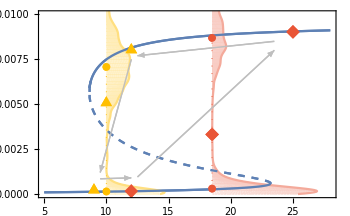

```mathematica
yrange=0.011;
vmax=0.01;
vmax2=0.01;
BifurcationFinal=Show[BifurcationPlot,ParametricPlot[{ConcListStochUp[[2]]+v PDF[upsmoothed,p],p},{p,0,yrange},{v,0,vmax},PlotStyle->{Lighter[ColorData[97,11],0.7]},BoundaryStyle->None],ParametricPlot[{ConcListStochUp[[2]]+vmax PDF[upsmoothed,p],p},{p,0,yrange},PlotStyle->{Lighter[ColorData[97,11],0.5],Thin}],ParametricPlot[{ConcListStochDown[[2]]+v PDF[downsmoothed,p],p},{p,0,yrange},{v,0,vmax2},PlotStyle->{Lighter[ColorData[97,8],0.7]},BoundaryStyle->None],ParametricPlot[{ConcListStochDown[[2]]+vmax2 PDF[downsmoothed,p],p},{p,0,yrange},PlotStyle->{Lighter[ColorData[97,8],0.5],Thin}],

Show[DetPlot,
ListPlot[{PlotDataStochUp,PlotDataStochDown},PlotStyle->{ColorData[97,11],ColorData[97,8]},PlotMarkers->{{◆,14},{▲,14}}],
ListPlot[{PlotBimodalUp,PlotBimodalDown},PlotStyle->{ColorData[97,11],ColorData[97,8]},PlotMarkers->{•,8}],
Graphics[{{Dotted,Thickness[0.002],ColorData[97,11],Line[{{18.5,BimodalUp[[1]]},{18.5,BimodalUp[[2]]}}]},{Dotted,Thickness[0.002],ColorData[97,8],Line[{{10,BimodalDown[[1]]},{10,BimodalDown[[2]]}}]}}],
Graphics[{Lighter[Gray,0.5],Arrow[{{9.5,0.00085},{12,0.0009}}],Arrow[{{12.5,0.00095},{23.5,0.008}}],Arrow[{{23.5,0.0085},{12.5,0.0077}}],Arrow[{{12,0.0075},{9.5,0.0012}}]}],
Frame->True,Evaluate@Join[plotOptionsBasic],ImageSize->350,BaseStyle->{FontFamily->"Times",FontSize->13},FrameLabel->MaTeX[{"\\mathrm{[c]_a}","\\mathrm{[p]_a}"},"FontSize"->14]]

,PlotRange->{{5,28}, {0,yrange-0.001}}]
```

```mathematica
BifurcationPlotResize=Show[ImportString[ExportString[BifurcationFinal,"PDF"],"PDF"],ImageSize->0.92*5.2*inch];
```

```mathematica
Export[FileNameJoin[{"Exports","Bifurcation.eps"}],BifurcationPlotResize];
```

```mathematica
Export[FileNameJoin[{"Exports","Bifurcation.pdf"}],BifurcationPlotResize];
```